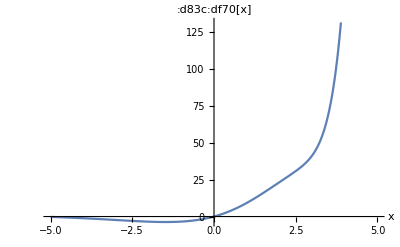
The Graphed Function: 2+ⅇ^x (-1+x)-ⅇ^x (1-3 x+x^2)+1/2 (-2+ⅇ^x (2+(-3+x) (-2+x) x))
-Graphics-

```mathematica
:d83d:dea5=2;
:d83d:de1f[:d83d:dc68‍:d83d:dcbb_,:d83d:dc16_,:d83d:dc10_]:=Integrate[:d83d:dc68‍:d83d:dcbb[:d83c:df84],{:d83c:df84,:d83d:dc16,:d83d:dc10}];
:d83c:df02☂[:d83c:df0a_]:=Series[:d83c:df0e*Exp[:d83c:df0e],{:d83c:df0e,:d83c:df0d,:d83c:df0a}];
:d83c:df20=Normal[:d83c:df02☂[:d83d:dea5]];
☣=Function[{:d83c:df0e,:d83c:df0d},#]&/@Level[:d83c:df20,1];
:d83d:dec0={};
Do[AppendTo[:d83d:dec0,:d83d:de1f[Function[:d83c:dfd1,Evaluate[☣[[:d83c:df0c]][:d83d:dea5,:d83c:dfd1]]],0,:d83c:dfc1]],{:d83c:df0c,Length@☣}]
:d83c:df7b=:d83d:dec0/.{List-> Plus};
:d83c:df70=Evaluate[:d83c:df7b/.{:d83c:dfc1-> #}]&;
Column[{Framed[Row[{Text@"The Graphed Function: ",Text[Style[:d83c:df70[x],TextAlignment->Center]]}]],Plot[:d83c:df70[:d83d:de09],{:d83d:de09,-5,5},AxesLabel->{Style["x",15,FontColor->Black],Style[":d83c:df70[x]",15,FontColor->Black]},ImageSize->Full]},ItemSize->{Scaled[.5],Automatic}]
```